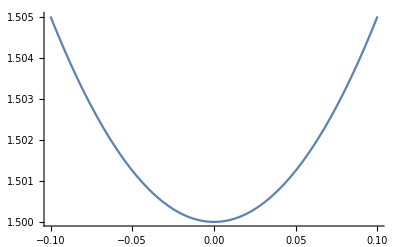

```mathematica
Plot[1/2+a^2/(1-Exp[-a^2]),{a,-0.1,0.1},PlotRange->All]
```

```mathematica
F[a_]:=1/2+a^2/(1-Exp[-a^2])
```

```mathematica
Limit[F[a],a->0]
```

3/2

```mathematica
D[A(3-2a^2)+L*Sqrt[4a^2-4a^4],a]
```

-4 a A+((8 a-16 a^3) L)/(2 √(4 a^2-4 a^4))

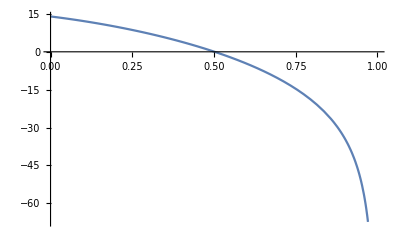

```mathematica
Plot[-4*4 a +(7*(8 a-16 a^3))/(2 √(4 a^2-4 a^4)),{a,0,1}]
L:=L
A:=A
```

```mathematica
Solve[-4 a A+((8 a-16 a^3) L)/(2 √(4 a^2-4 a^4))==0,a]
```

{{a→-(√(A^2/(A^2+L^2)+L^2/(A^2+L^2)-(√(A^2 (A^2+L^2)))/(A^2+L^2)))/(√2)},{a→(√(A^2/(A^2+L^2)+L^2/(A^2+L^2)-(√(A^2 (A^2+L^2)))/(A^2+L^2)))/(√2)},{a→-(√(A^2/(A^2+L^2)+L^2/(A^2+L^2)+(√(A^2 (A^2+L^2)))/(A^2+L^2)))/(√2)},{a→(√(A^2/(A^2+L^2)+L^2/(A^2+L^2)+(√(A^2 (A^2+L^2)))/(A^2+L^2)))/(√2)}}